```mathematica
data=Import["overfin.tsv"]
```

{{byCount,16407,-7.4531,41.5545,72.4,16.831},{byCount,16467,-7.4532,41.5546,72.6,16.4975},{byCount,16527,-7.4532,41.5546,72.7,16.831},{byCount,16587,-7.4533,41.5546,72.7,16.4975},8600,{byCount,75618,-7.4503,41.5533,76.3,48.2327},{byCount,75678,-7.4503,41.5533,76.2,48.3163},{byCount,75738,-7.4503,41.5533,76.2,49.2364}}
 |  |  |  |

```mathematica
foo=data[[All,1;; 6]]
```

{{byCount,16407,-7.4531,41.5545,72.4,16.831},{byCount,16467,-7.4532,41.5546,72.6,16.4975},{byCount,16527,-7.4532,41.5546,72.7,16.831},{byCount,16587,-7.4533,41.5546,72.7,16.4975},8600,{byCount,75618,-7.4503,41.5533,76.3,48.2327},{byCount,75678,-7.4503,41.5533,76.2,48.3163},{byCount,75738,-7.4503,41.5533,76.2,49.2364}}
 |  |  |  |

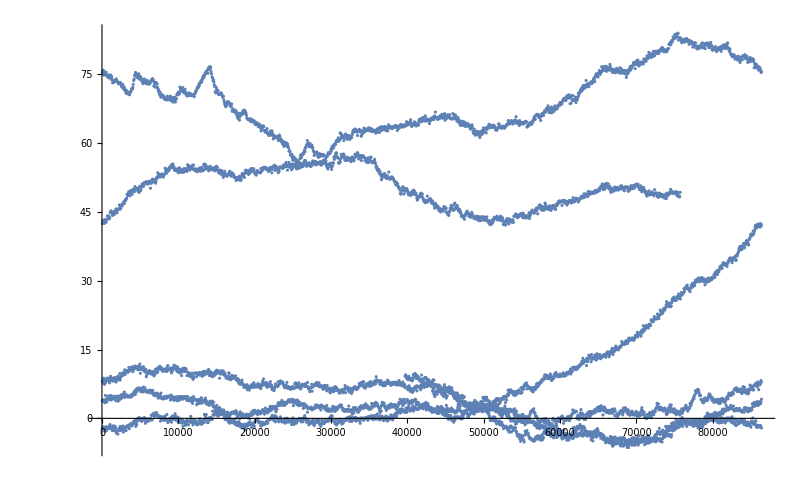

```mathematica
ListPlot[ data[[ 800;; ,{2,6}]] ]
```

```mathematica
Hue[0.88]
ColorData["Rainbow"][0.97]
(ColorData["Rainbow"][0.97]&)[1]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
List

[Rescale[#2,{-1,1}]]&)   ColorFunction->Function[{x},(ColorData["Rainbow"][0.97])]

ColorFunction->(ColorData["Rainbow"][0.88]&)

ColorFunctionScaling->False,[Rescale[#3/100000,{0,1}]]
```